```mathematica
ρ[r_]:=ρ0 Exp[-(r/rc-1)^2/2]+ρ1
```

(cs^2 r (-r+rc) ρ0)/(rc^2 (ρ0+ⅇ^(1/2 (-1+r/rc)^2) ρ1))

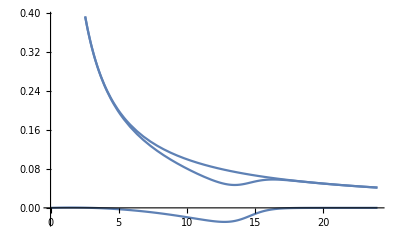

```mathematica
cs^2 r/ρ[r] ρ'[r]//FullSimplify
Plot[{%,1/r,%+1/r}/.{rc->3,ρ0->1,ρ1->0.001,cs->0.05},{r,0,24}]
```

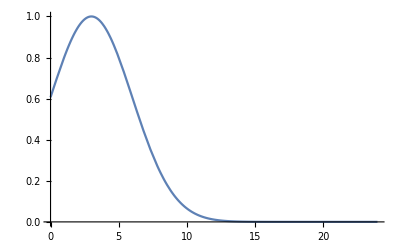

```mathematica
Plot[ρ[r]/.{rc->3,ρ0->1,ρ1->0.0001,cs->0.05},{r,0,24}]
```

```mathematica
(cs^2 r (-r+rc) (ρ[r]-ρ1))/(rc^2 ρ[r])==(cs^2 r (-r+rc) ρ0)/(rc^2 (ρ0+ⅇ^(1/2 (-1+r/rc)^2) ρ1))//FullSimplify
```

True